# Notebook 5 :Compartmental Modeling

The aim of this lab notebook is to give users ideas of the basic principles of compartmental modeling through investigating a complex multi-compartmental model.

1. Compartmental Modeling :

#### Biological cell (especially eukaryotic cell, see the graph below) is composed of many compartments : cytosol, mitochondria, nucleus, endoplasmic reticulum, etc. There are always lots of exchange of organic and inorganic sunstances among those compartments. To address these frequent substance exchange activities and correctly model complex cellular processes involving multiple compartments, compartmental modeling becomes inevitable.

### Basic Principles

Assume a model involves the exchange of certain substance (ion, enzyme, etc.) among n compartments, if we denote the concentration of this substance in the ith compartment as C_i(1≤i≤n), then typically a multi-compartmental model can be framed as :

dC_i/dt=α_i (∑J_in-∑J_out)   (1≤i≤n)
 
 where α_i is a parameter related to the volume of the ith compartment, ∑J_in denotes all the influx into this compartment, ∑J_out denotes the sum of all the outflux from this compartment.

### Example : Modeling Complex Calcium Oscillations

To get a flavor of  compartmental modeling, let us look at a comprehensive compartmental model for calcium oscillations (Marhl, et al., Biosystems 57, pp.75-86 (2000)). The schematic graph of the model is as follows :

This model involves calcium ion (Ca^(2+) ) exchange among three compartments : cytosol, mitochondria and ER(endoplasmic reticulum). The system consists of the following three equations for the Ca^(2+) concentrations in these three compartments respectively (For details, please see the original paper) :

          (1)
                                                                          (2)
                                                                                                   (3)

Please note that various Ca^(2+)  exchange activities have been included in this model. For example, J_leak represents the leak flux from ER into the cytosol , mathematically it is modeled as Jleak=kleak(CaER-Cacyt).  Since J_leak is an influx into cytosol, it has a positive contribution to the Ca^(2+) concentration change in cytosol (see the above first equation). At the same time, J_leak is an outflux from ER, it has a negative contribution to the Ca^(2+) concentration change in ER (see the above second equation). 

By using the parameters in the original paper, we can simulate cytosolic calcium bursting (in bursting, phases of high frequency oscillations are separated by phases of quiescence, in a pattern that occur at regular intervals) and chaos. The following Mathematica codes reproduce Fig.2 of the original paper which is simulating cytosolic calcium bursting :

```mathematica
Clear[t,x,y,z];Kch=4100;
solution=NDSolve[{x'[t]==Kch (x[t]^2 (y[t]-x[t]))/(25+x[t]^2)+0.05 (y[t]-x[t])-20 x[t]+(125 x[t]^2/(x[t]^2+25)+0.00625) z[t] -300 x[t]^8/(0.8^8 +x[t]^8)+0.01 (90-x[t] -4 y[t]-4 z[t])-0.1 x[t] (30+x[t]+4 y[t]+4 z[t]),y'[t]==- 1/4 (Kch (x[t]^2 (y[t]-x[t]))/(25+x[t]^2)+0.05 (y[t]-x[t])-20 x[t]),z'[t]==- 1/4 ((125 x[t]^2/(x[t]^2+25)+0.00625) z[t] -300 x[t]^8/(0.8^8 +x[t]^8)),x[0]==0.3,y[0]==0.2,z[0]==1.0},{x,y,z},{t,0,300},MaxSteps->30000];Plot[Evaluate[x[t]/.solution],{t,100,150},PlotRange->All,AxesLabel->{"t (Sec)","Ca_cyt (μM)"}];
ParametricPlot[Evaluate[{z[t],x[t]}/.solution],{t,100,140},PlotPoints->3000,PlotRange->All];
```

2. Exercises

### Exercise 1 : Limit Cycle and Chaotic behavior

By change the parameter Kch in the above example, show that the Ca2+ bursting oscillations will exhibit two-folded limit cycle and chaotic behavior. (Hint: read the legends in Fig.4 and Fig.5 of the original paper)

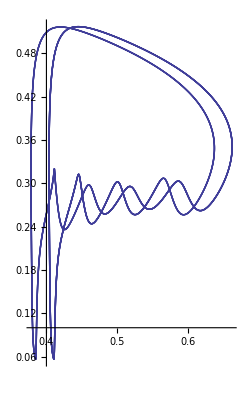

```mathematica
Clear[t,x,y,z];Kch=4000;
solution=NDSolve[{x'[t]==Kch (x[t]^2 (y[t]-x[t]))/(25+x[t]^2)+0.05 (y[t]-x[t])-20 x[t]+(125 x[t]^2/(x[t]^2+25)+0.00625) z[t] -300 x[t]^8/(0.8^8 +x[t]^8)+0.01 (90-x[t] -4 y[t]-4 z[t])-0.1 x[t] (30+x[t]+4 y[t]+4 z[t]),y'[t]==- 1/4 (Kch (x[t]^2 (y[t]-x[t]))/(25+x[t]^2)+0.05 (y[t]-x[t])-20 x[t]),z'[t]==- 1/4 ((125 x[t]^2/(x[t]^2+25)+0.00625) z[t] -300 x[t]^8/(0.8^8 +x[t]^8)),x[0]==0.3,y[0]==0.2,z[0]==1.0},{x,y,z},{t,0,300},MaxSteps->30000];ParametricPlot[Evaluate[{z[t],x[t]}/.solution],{t,100,200},PlotPoints->3000,PlotRange->All]
```

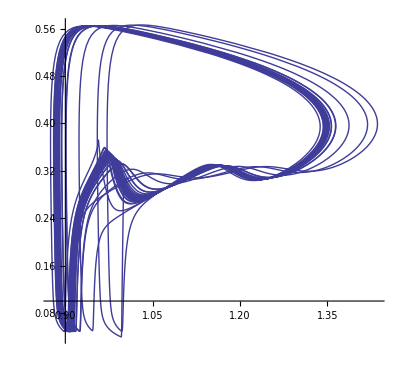

```mathematica
Clear[t,x,y,z];Kch=2950;
solution=NDSolve[{x'[t]==Kch (x[t]^2 (y[t]-x[t]))/(25+x[t]^2)+0.05 (y[t]-x[t])-20 x[t]+(125 x[t]^2/(x[t]^2+25)+0.00625) z[t] -300 x[t]^8/(0.8^8 +x[t]^8)+0.01 (90-x[t] -4 y[t]-4 z[t])-0.1 x[t] (30+x[t]+4 y[t]+4 z[t]),y'[t]==- 1/4 (Kch (x[t]^2 (y[t]-x[t]))/(25+x[t]^2)+0.05 (y[t]-x[t])-20 x[t]),z'[t]==- 1/4 ((125 x[t]^2/(x[t]^2+25)+0.00625) z[t] -300 x[t]^8/(0.8^8 +x[t]^8)),x[0]==0.3,y[0]==0.2,z[0]==1.0},{x,y,z},{t,0,300},MaxSteps->30000];ParametricPlot[Evaluate[{z[t],x[t]}/.solution],{t,0,300},PlotPoints->3000,PlotRange->All]
```

### Exercise 2 : Slight Model Modifications

Lets us make some slight modifications to the above multi-compartmental model:
(i).  Assume that due to deletion of the corresponding gene, the channel protein through which Ca2+ is transported from ER into cytosol does not exist anymore, how should we rewrite the main three equations.
(ii). Assume that now another compartment named as Golgi complex is further included into the model : it also has a  Ca2+ influx from cytosol through a pump and a  Ca2+  leakflux into the cytosol,  how should we rewrite the main equations.
(ii).(optional) Read the orginal paper, please give a detailed clear explanation of the different terms in three main equations of the original multi-compartmental model.